```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
evo1=Import["./Evolutions/gol_1000s.mat"][[1]];
evo2=Import["./Evolutions/gol_nca_2n.mat"][[1]];
```

```mathematica
diferences=Total[Unitize[#1-#2],2]&@@@Transpose[{evo1,evo2}];
```

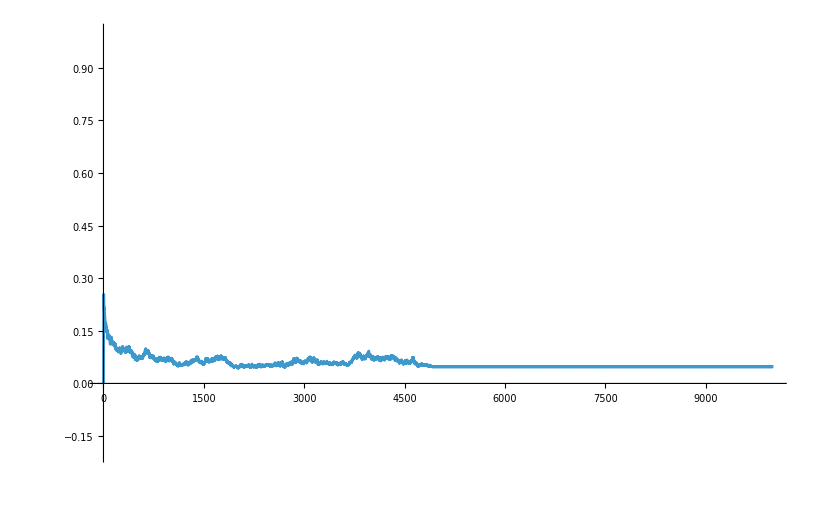

```mathematica
ListLinePlot[diferences/(100*100),PlotRange->{All,{-0.2,1}}]
```

```mathematica
Exit[]
```

```mathematica
evo1=Import["./Evolutions/gol_1000s.mat"][[1]];
evo2=CellularAutomaton["GameOfLife",evo1[[1]],1000];
```

```mathematica
plot1=ArrayPlot[evo1[[-1]]];
plot2=ArrayPlot[evo2[[-1]]];
plot3=ListPlot[Map[Total[#,2]&,Abs[evo1-evo2]],PlotLabel->"Diferencia absoluta por paso",AxesLabel->{"Paso","Pixeles discordantes"}];
```

```mathematica
Export["prueba_life_1.png",plot1,"PNG",ImageResolution->150];
Export["prueba_life_2.png",plot2,"PNG",ImageResolution->150];
Export["prueba_life_3.png",plot3,"PNG",ImageResolution->150];
```

True